# Local Optimization on the Gaussian manifold

This notebook is intended as a guide to using the optimization algorithm performing gradient descent over the manifold of pure bosonic or fermionic Gaussian states.
Throughout the notebook, we have adopted the following conventions:

	- Function to be optimised: F=f(M,J_0) where M is the transformation acting on the initial state J_o
	- Gradient of function to be optimised: ∇=df(M,J_0,K,G^-1) where K is the Lie algebra basis and G^-1 is the natural metric of the manifold

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]<>"Packages (.m files)"];
<<GaussianOptimization`
```

# The GaussianOptimization.m package and its functions

All functions included in the package, in alphabetical order:

```mathematica
?"GaussianOptimization`*"
```

## Optimization algorithm

```mathematica
?GOOptimize
```

{ F_final , M_final , N_corrections , {F} , {all F} , {|∇|} }=GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]

ProblemSpecific={f,df} 
SystemSpecific={J_0,listM_0,K,G}
ProcedureSpecific={tol_F,tol_∇,lim_iterations ,step size sub-routine,track all trajectories?}

## Basic Tools and Fundamental definitions

Symplectic forms and Covariance matrices

For Bosonic states

```mathematica
?GOΩqpqp
```

```mathematica
?GOΩqqpp
```

```mathematica
?GOΩaabb
```

```mathematica
?GOΩabab
```

For Fermionic states

```mathematica
?GOGqpqp
```

```mathematica
?GOGqqpp
```

```mathematica
?GOGaabb
```

```mathematica
?GOGabab
```

Transforming between structures

```mathematica
?GOTransformGtoJ
```

```mathematica
?GOTransformΩtoJ
```

```mathematica
?GOTransformJtoG
```

```mathematica
?GOTransformJtoΩ
```

Basis Transformation matrices

We provide basis transformation matrices for transformations between four bases (note that b_i are the respective annihilation operators):
 (q_1,p_1,q_2,p_2,...) 	(q_1,q_2,...,p_1,p_2,...)	(a_1,b_1,a_2,b_2,...)	(a_1,a_2,...,b_1,b_2,...)

where we have defined:		a_i=1/(√2)(q_i+ⅈ p_i)  and   b_i=1/(√2)(q_i-ⅈ p_i)

Re-ordering

```mathematica
?GOqqppFROMqpqp
```

```mathematica
?GOqpqpFROMqqpp
```

```mathematica
?GOaabbFROMabab
```

```mathematica
?GOababFROMaabb
```

position / momentum → annihilation / creation operators

```mathematica
?GOababFROMqpqp
```

```mathematica
?GOaabbFROMqpqp
```

```mathematica
?GOababFROMqqpp
```

```mathematica
?GOaabbFROMqqpp
```

annihilation / creation operators → position / momentum

```mathematica
?GOqpqpFROMabab
```

```mathematica
?GOqqppFROMabab
```

```mathematica
?GOqpqpFROMaabb
```

```mathematica
?GOqqppFROMaabb
```

Lie algebra bases

All Lie algebra bases are generated in the basis  (q_1,p_1,q_2,p_2,...)  by convention

```mathematica
?GOSpBasis
```

```mathematica
?GOSpBasisNoUN
```

```mathematica
?GOSpBasisNoU1
```

```mathematica
?GOOBasis
```

We can also construct a compound Lie algebra basis for a system that is divided into two subsystems:

```mathematica
?GOCompoundBasis
```

Metrics for the symplectic and orthogonal manifolds

```mathematica
?GOMetricSp
```

```mathematica
?GOMetricO
```

Generating random Transformations

```mathematica
?GORandomTransformation
```

Tools for computational efficiency

```mathematica
?GOapproxExp
```

```mathematica
?GOlogfunction
```

```mathematica
?GOConditionalLog
```

```mathematica
?GOinvMSp
```

## Applications implemented in GaussianOptimization.m

Purifications and the standard form

```mathematica
?GOExtractStdFormG
```

```mathematica
?GOExtractStdFormΩ
```

```mathematica
?GOPurifyStandardGBoson
```

```mathematica
?GOPurifyStandardJBoson
```

```mathematica
?GOPurifyStandardΩFermion
```

```mathematica
?GOPurifyStandardJFermion
```

Entanglement of Purification

```mathematica
?GORestrictionAA
```

```mathematica
?GOEoPBos
```

```mathematica
?GOEoPgradBos
```

```mathematica
?GOEoPFerm
```

```mathematica
?GOEoPgradFerm
```

Complexity of Purification

```mathematica
?GOCoPBos
```

```mathematica
?GOCoPgradBos
```

Energy of quadratic Hamiltonians

```mathematica
?GOenergyBos
```

```mathematica
?GOenergygradBos
```

```mathematica
?GOenergyFerm
```

```mathematica
?GOenergygradFerm
```

# Selected examples: EoP and CoP

## Bosonic Entanglement of Purification (EoP)

#### 0. Initialize definitions: Functions to generate the initial covariance matrices for a lattice free scalar field theory

```mathematica
FourierMatrixElement[N_]:=Function[{k,x},Exp[I 2 Pi x k /N]/Sqrt[N]];
DispersionRelation[m_,N_,l_]:=Function[{k},Sqrt[m^2+4/l^2  (Sin[Pi k/N])^2]];
```

```mathematica
FT[n_]:=Module[{f,pos,val},
f=FourierMatrixElement[n];
pos=Table[{x,k},{k,n},{x,n}]//Flatten[#,1]&;
val=Table[f[k,x]//N,{k,n},{x,n}]//Flatten[#,1]&;
SparseArray[pos->val]];
```

```mathematica
Diag[m_,n_,l_]:=Module[{ω},
ω=DispersionRelation[m,n,l];
DiagonalMatrix[Table[ω[k],{k,n}]]];
```

```mathematica
invDiag[m_,n_,l_]:=Module[{ω},
ω=DispersionRelation[m,n,l];
DiagonalMatrix[Table[1/ω[k],{k,n}]]];
```

```mathematica
CM[N_,m_,l_]:=Module[{F,D,invD,G,Tr},
F=FT[N];D=Diag[m,N,l]; invD=invDiag[m,N,l];
G=ArrayFlatten[({{F.D.ConjugateTranspose[F], 0}, {0, F.invD.ConjugateTranspose[F]}})]//Chop//SparseArray];
```

```mathematica
partialCM[N_,m_,l_,d_,dim1_,dim2_]:=
Module[{dim, halfdim, bigCM, indices1, indices2,indices, partialCM, Tr},

bigCM=CM[N,m,l];
dim=Length[bigCM]; halfdim=dim/2;

indices1=Thread[{Table[x,{x,dim1}],Table[x+halfdim,{x,dim1}]}]//Flatten[#,1]&;
indices2=Thread[{Table[dim1+d+x,{x,dim2}],Table[dim1+d+x+halfdim,{x,dim2}]}]//Flatten[#,1]&;

indices=Join[indices1,indices2];

partialCM=bigCM[[indices,indices]]];
```

#### 1. Generate the initial mixed state covariance matrix

Note: The functions used to define the initial mixed state covariance matrix below are beyond the scope of the GaussianOptimization.m package and are not included in it.
In the example below, the mixed state is obtained for a system with total number of lattice sites 100 with 3 sites per subsystem in the initial system, mass term 0.1, lattice spacing 1, 
and no lattice sites separating the subsystems.

```mathematica
CM0=partialCM[100,.1,1,0,3,3]; CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315
-0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

#### 2. Generate the purified state complex structure (in this case for a minimal purification)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0];
J0=GOPurifyStandardJBoson[rlist,6,"qpqp"];
```

#### 3. Generate a list of the starting points for the optimization (in this case 50 random transformations)

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GORandomTransformation[12,"GOSpBasis"]}}]//SparseArray,{50}];
```

#### 4. Define the problem-specific input arguments

```mathematica
Restriction=GORestrictionAA[{3,3,3,3}];
function=GOEoPBos[Restriction]; gradient=GOEoPgradBos[Restriction];
ProblemSpecific={function,gradient};
```

#### 5. Define the system-specific input arguments

```mathematica
LieBasis=GOCompoundBasis[{"None","GOSpBasis"},{6,6}];
metric=GOMetricSp[LieBasis,J0];

SystemSpecific={J0,M0List,LieBasis,metric};
```

#### 6. Define the procedure-specific input arguments

```mathematica
stepcorrection[s_]:=s/2;
ProcedureSpecific={10^-6,10^-10,∞,stepcorrection,False};
(* Here we specify that all 50 initial trajectories should be pursured until convergence *)
```

#### 7. Run the Optimization

```mathematica
{Time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

Reason for termination: Function value tolerance reached

#### 8. Evaluate the result

Time taken: 7.88649

Final value: {0.379655}

Number of iterations: {75}

Number of total corrections: 63

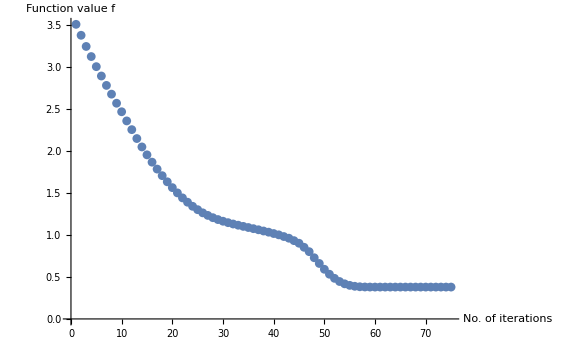

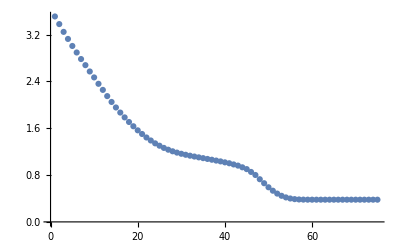

```mathematica
Print["Time taken: ",Time];
Print["Final value: ",Result[[1,All]]];
Print["Number of iterations: ",Length/@Result[[4]]];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[#, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]&/@Result[[4]]
(* We plot all items in the finalElist object in the result to ensure a correct plot in the case of multiple results *)
ListPlot/@Result[[5]]
```

## Bosonic Complexity of Purification (CoP)

#### 0. Initialize definitions: Functions to generate the initial covariance matrices for a lattice free scalar field theory

```mathematica
FourierMatrixElement[N_]:=Function[{k,x},Exp[I 2 Pi x k /N]/Sqrt[N]];
DispersionRelation[m_,N_,l_]:=Function[{k},Sqrt[m^2+4/l^2  (Sin[Pi k/N])^2]];
```

```mathematica
FT[n_]:=Module[{f,pos,val},
f=FourierMatrixElement[n];
pos=Table[{x,k},{k,n},{x,n}]//Flatten[#,1]&;
val=Table[f[k,x]//N,{k,n},{x,n}]//Flatten[#,1]&;
SparseArray[pos->val]];
```

```mathematica
Diag[m_,n_,l_]:=Module[{ω},
ω=DispersionRelation[m,n,l];
DiagonalMatrix[Table[ω[k],{k,n}]]];
```

```mathematica
invDiag[m_,n_,l_]:=Module[{ω},
ω=DispersionRelation[m,n,l];
DiagonalMatrix[Table[1/ω[k],{k,n}]]];
```

```mathematica
CM[N_,m_,l_]:=Module[{F,D,invD,G,Tr},
F=FT[N];D=Diag[m,N,l]; invD=invDiag[m,N,l];
G=ArrayFlatten[({{F.D.ConjugateTranspose[F], 0}, {0, F.invD.ConjugateTranspose[F]}})]//Chop//SparseArray];
```

```mathematica
partialCM[N_,m_,l_,d_,dim1_,dim2_]:=
Module[{dim, halfdim, bigCM, indices1, indices2,indices, partialCM, Tr},

bigCM=CM[N,m,l];
dim=Length[bigCM]; halfdim=dim/2;

indices1=Thread[{Table[x,{x,dim1}],Table[x+halfdim,{x,dim1}]}]//Flatten[#,1]&;
indices2=Thread[{Table[dim1+d+x,{x,dim2}],Table[dim1+d+x+halfdim,{x,dim2}]}]//Flatten[#,1]&;

indices=Join[indices1,indices2];

partialCM=bigCM[[indices,indices]]];
```

#### 1. Generate the initial mixed state covariance matrix

Note: The functions used to define the initial mixed state covariance matrix below are beyond the scope of the GaussianOptimization.m package and are not included in it.
In the example below, the mixed state is obtained for a system with total number of lattice sites 100 with 3 sites per subsystem in the initial system, mass term 0.1, lattice spacing 1, 
and no lattice sites separating the subsystems.

```mathematica
CM0=partialCM[100,.1,1,0,3,3]; CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315
-0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

#### 2. Generate the purified state complex structure (in this case for a minimal purification)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0];
JT=GOPurifyStandardJBoson[rlist,6,"qpqp"];
JR0=GOTransformGtoJ[IdentityMatrix[24],"qpqp","qpqp"];
```

#### 3. Generate a list of the starting points for the optimization (in this case 10 random transformations)

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GORandomTransformation[12,"GOSpBasis"]}}]//SparseArray,{10}];
```

#### 4. Define the problem-specific input arguments

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
ProblemSpecific={function,gradient};
```

#### 5. Define the system-specific input arguments

```mathematica
LieBasis=GOCompoundBasis[{"None","GOSpBasis"},{6,6}];
metric=GOMetricSp[LieBasis,JR0];

SystemSpecific={JR0,M0List,LieBasis,metric};
```

#### 6. Define the procedure-specific input arguments

```mathematica
stepcorrection[s_]:=s/2;
ProcedureSpecific={10^-6,10^-10,∞,stepcorrection,False};
```

#### 7. Execute the optimization

```mathematica
{Time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

Reason for termination: Function value tolerance reached

#### 8. Evaluate the result

Time taken: 9.7776

Final value: {1.0354,1.0354}

Number of iterations: {7,7}

Number of total corrections: 2

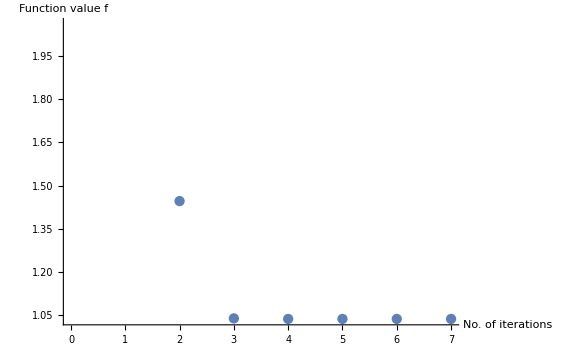

```mathematica
Print["Time taken: ",Time];
Print["Final value: ",Result[[1,All]]];
Print["Number of iterations: ",Length/@Result[[4]]];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4,1]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
(* We plot all items in the finalElist object in the result to ensure a correct plot in the case of multiple results *)
```

```mathematica
(* This looks like just one trajectory but it is in fact four identical trajectories! *)
```

## Fermionic Entanglement of Purification (EoP)

#### 0. Initialize definitions: Functions to generate the initial covariance matrices for a lattice free scalar field theory

```mathematica
ϵ[k_]=√(h^2+2h J Cos[k]+J^2+(γ^2-1)J^2 Sin[k]^2);
a[k_]=-J Cos[k]-h;
b[k_]=γ J Sin[k];
u[k_]=(ϵ[k]+a[k])/(√(2ϵ[k](ϵ[k]+a[k])));
v[k_]=(ⅈ b[k])/(√(2ϵ[k](ϵ[k]+a[k])));
Sf[xx_]=-(1+xx)/2 Log[2,(1+xx)/2]-(1-xx)/2 Log[2,(1-xx)/2];
ϵmin[J_,h_,γ_]:=√(γ^2(J^2+h^2/(γ^2-1)));
ϵmax[J_,h_,γ_]:=√(J^2+2h J+h^2);
```

#### 1. Generate the initial mixed state covariance matrix

Note: The functions used to define the initial mixed state covariance matrix below are beyond the scope of the GaussianOptimization.m package and are not included in it.
In this case we are generating a covariance matrix for a system with a total of 10 lattice sites and partitioning it into two adjacent subsystems containing 2 lattice sites each.

```mathematica
NN=10;J=1;h=.5;γ=.5;
u[0]=0;v[0]=ⅈ;u[π]=1;v[π]=0;
Ωblock=1/NN Table[Sum[(Abs[v[2π k/NN]]^2-Abs[u[2π k/NN]]^2)Cos[2π k(j-l)/NN]+2Im[v[2π k/NN]u[2π k/NN]]Sin[2π k(j-l)/NN],{k,0,NN-1}],{j,1,NN},{l,1,NN}];
ΩΩ=ArrayFlatten[({{0, Ωblock}, {-Transpose[Ωblock], 0}})];JJ=ΩΩ;

dim=10; dim1=2; dim2=2; d=0;
indices1=Thread[{Table[x,{x,dim1}],Table[x+dim,{x,dim1}]}]//Flatten[#,1]&;
indices2=Thread[{Table[dim1+d+x,{x,dim2}],Table[dim1+d+x+dim,{x,dim2}]}]//Flatten[#,1]&;
indices=Join[indices1,indices2];

Tran=GOqpqpFROMqqpp[dim]; ΩΩqpqp=Tran.ΩΩ.Transpose[Tran];
Ω0=ΩΩqpqp[[indices,indices]]; Ω0//MatrixForm
```

(0. | 0. | 0.297177 | -0.0421826 | 0. | 0. | 0.125706 | 0.0605457
0. | 0. | -0.0421826 | 0.297177 | 0. | 0. | 0.0605457 | 0.125706
-0.297177 | 0.0421826 | 0. | 0. | -0.885027 | -0.0108273 | 0. | 0.
0.0421826 | -0.297177 | 0. | 0. | -0.0108273 | -0.885027 | 0. | 0.
0. | 0. | 0.885027 | 0.0108273 | 0. | 0. | 0.297177 | -0.0421826
0. | 0. | 0.0108273 | 0.885027 | 0. | 0. | -0.0421826 | 0.297177
-0.125706 | -0.0605457 | 0. | 0. | -0.297177 | 0.0421826 | 0. | 0.
-0.0605457 | -0.125706 | 0. | 0. | 0.0421826 | -0.297177 | 0. | 0.)

#### 2. Generate the purified state complex structure (in this case for a minimal purification)

```mathematica
{rlist,MTra}=GOExtractStdFormΩ[Ω0];
J0=GOPurifyStandardJFermion[rlist,4,"qpqp"];
```

#### 3. Generate a list of the starting points for the optimization (in this case 10 random transformations)

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GORandomTransformation[8,"GOOBasis"]}}]//SparseArray,{10}];
```

#### 4. Define the problem-specific input arguments

```mathematica
Restriction=GORestrictionAA[{2,2,2,2}];
function=GOEoPFerm[Restriction]; gradient=GOEoPgradFerm[Restriction];
ProblemSpecific={function,gradient};
```

#### 5. Define the system-specific input arguments

```mathematica
LieBasis=GOCompoundBasis[{"None","GOOBasis"},{4,4}];
metric=GOMetricO[LieBasis];

SystemSpecific={J0,M0List,LieBasis,metric};
```

#### 6. Define the procedure-specific input arguments

```mathematica
stepcorrection[s_]:=s/2;
ProcedureSpecific={10^-9,10^-10,∞,stepcorrection,False};
```

#### 7. Run the Optimization

```mathematica
Result=GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific];
```

Reason for termination: Function value tolerance reached

#### 8. Evaluate the result

Final value: {0.751647}

Number of iterations: {30}

Number of total corrections: 57

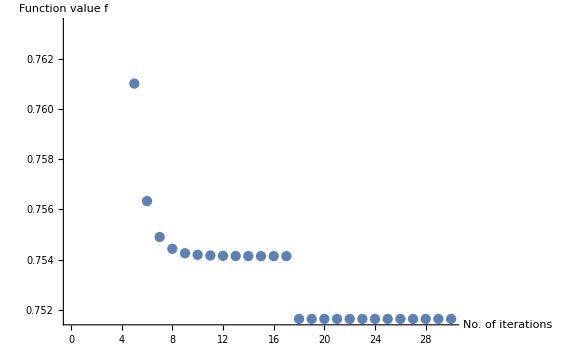

```mathematica
Print["Final value: ",Result[[1,All]]];
Print["Number of iterations: ",Length/@Result[[4]]];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[#, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]&/@Result[[4]]
(* We plot all items in the finalElist object in the result to ensure a correct plot in the case of multiple results *)
```